```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/choice_question/choice_question.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/choice_question/import.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/choice_question/~$choice_question.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/choice_question/~$import.xlsx}

```mathematica
importfile = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/choice_question/import.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"t"->(Around[#t,#dt]&),"ln"->(Around[#ln,#dln]&)|>]
```

Dataset[<>]

```mathematica
line1=LinearModelFit[Normal@dataset1[All,{"t","ln"}/*Values],{1,x},x]
line1["ParameterTable"]
```

FittedModel[1.26486+0.0638886 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.26486 | 0.0390652 | 32.3783 | 2.90563×10^-12
x | 0.0638886 | 0.00198939 | 32.1147 | 3.17625×10^-12

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"t"->(Around[#t,#dt]&),"ln"->(Around[#ln,#dln]&)|>]
```

Dataset[<>]

```mathematica
line2=LinearModelFit[Normal@dataset2[All,{"t","ln"}/*Values],{1,x},x]
line2["ParameterTable"]
```

FittedModel[1.45192+0.0527579 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.45192 | 0.0617211 | 23.5238 | 2.08157×10^-11
x | 0.0527579 | 0.00306559 | 17.2097 | 7.99836×10^-10

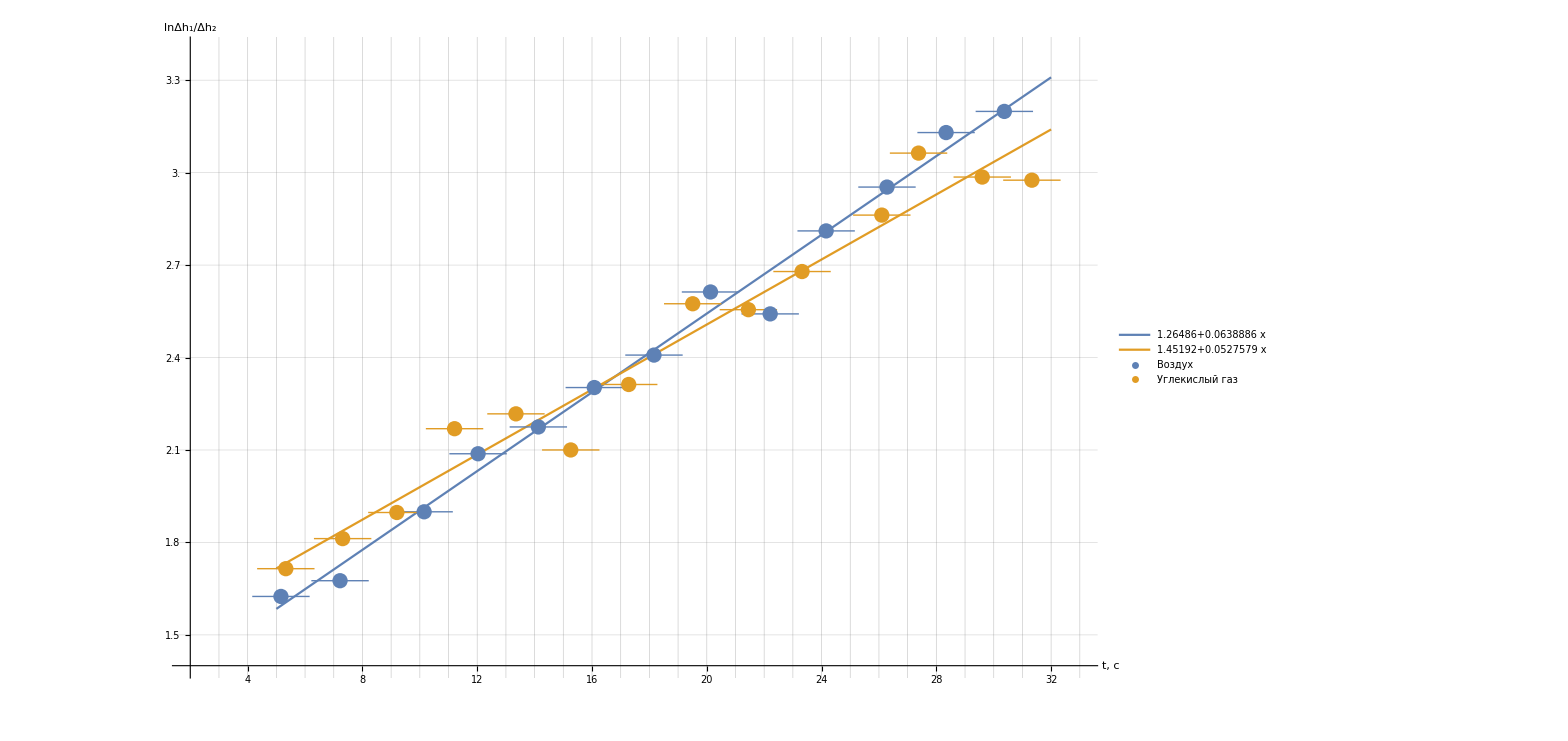

```mathematica
Show[
Plot[
{line1@x,line2@x},
{x,5,32},
AxesLabel->{Style["t, c", Large],Style["lnΔh_1/Δh_2",20]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,40,1],Range[0,10,0.05]},
PlotRange->{{2,33},{1.4,3.4}},
Ticks-> {Range[0,50,2],Range[0,5,0.1]},
TicksStyle->15,
PlotLegends->Placed[
LineLegend
[
Automatic,
Normal/@{line1,line2},
LegendFunction->Framed,
LabelStyle->{FontSize->18}
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset1WithErrs,dataset2WithErrs},
PlotLegends->Placed[LineLegend[
Automatic,
{"Воздух","Углекислый газ"},
LegendMarkerSize->15,
LegendFunction->Framed,
LabelStyle->{FontSize->18}
],
{Scaled[0.8],Scaled[0.3]}
]
]
]
```

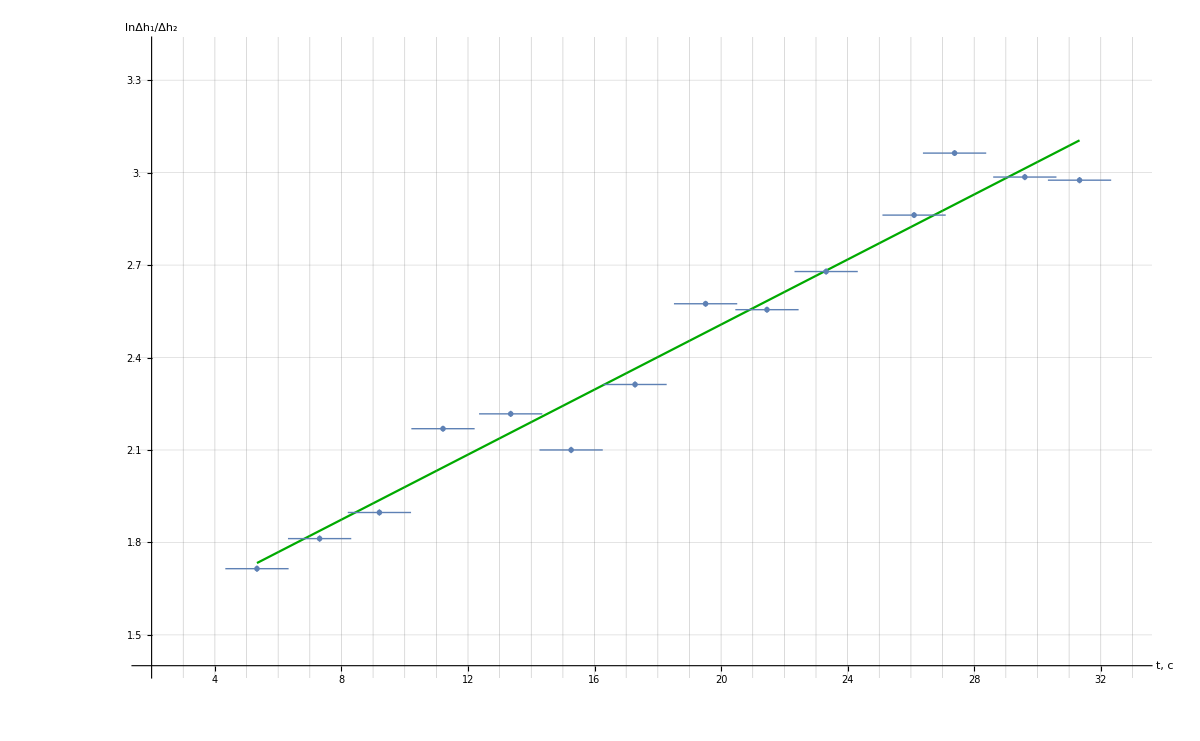

```mathematica
Show[
Plot[
{line2@x},
{x,5.33,31.33},
AxesLabel->{Style["t, c", Large],Style["lnΔh_1/Δh_2",20]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,40,1],Range[0,10,0.05]},
PlotRange->{{2,33},{1.4,3.4}},
Ticks-> {Range[0,50,2],Range[0,5,0.1]},
TicksStyle->15,
PlotStyle->Darker[Green]
],
ListPlot[
dataset2WithErrs,
PlotMarkers->{Graphics[{Darker[Green],Disk[{0,0},Scaled[.03]]}]}
]
]
```